```mathematica
Clear["Global`*"];
Needs["EcoEvo`"];
```

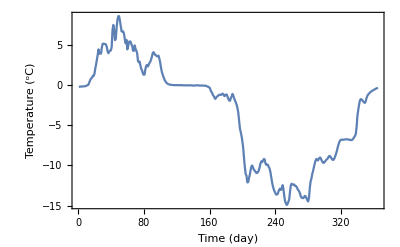

```mathematica
(*Importing Imnavait 20cm depth dataset and converting to daily timeseries*)
dat=Import["/Users/logangonzalez/Downloads/Imnaviat_temp.csv"];
cm20avg=List[];
Do[{AppendTo[cm20avg,Mean[{dat[[i]][[2]],dat[[i]][[3]]}]]},{i,2,23842}];
dataDiurnal=List[];
Do[AppendTo[dataDiurnal,Mean[cm20avg[[24 i+1;;24 i+24]]]],{i,0,364}];
ListPlot[dataDiurnal,Joined->True,Frame->True,FrameLabel->{"Time (day)","Temperature (^oC)"}]
```

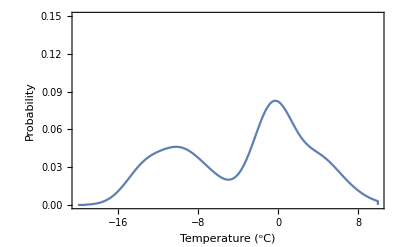

-3.36185

```mathematica
(*Probability distribution for temperatures experienced in Imnavait dataset*)
SmoothHistogram[dataDiurnal,PlotRange->{{-20,10},{0,.15}},Frame->True,Axes->None,FrameLabel->{"Temperature (^oC)","Probability"}]
Mean[dataDiurnal](*calculating average temperature of the Imnavait 20cm dataset*)
```

# Fourier series fit

```mathematica
(*fitting a Fourier series to the Imnaviat dataset*)
model=Fit[dataDiurnal,Table[Sin[(π n )/365   t],{n,1,100}],t];
fourierfit[t_]:=ResourceFunction["TrigFit"][dataDiurnal,100,{t,364}];

(*plotting residuals and calculating RMSE for the Fourier series fit*)
```

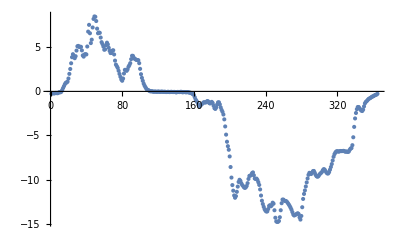

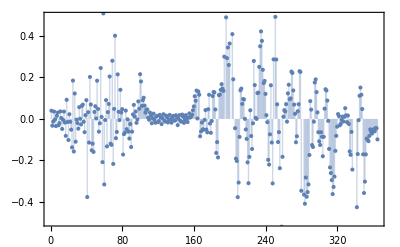

0.201274

```mathematica
(*a list was generated from the Fourier series fit in order to make comparisons with each datapoint from the Imnavait dataset*)
fourierFitList={};
Do[
AppendTo[fourierFitList,ResourceFunction["TrigFit"][dataDiurnal,100,{x,364}]/.x->i],{i,0,364}]
ListPlot[fourierFitList]

ListPlot[dataDiurnal-fourierFitList,Frame->True,Filling->Axis]
RootMeanSquare[dataDiurnal-fourierFitList]
```

# LV model (Uses EcoEvo Package: https://github.com/cklausme/EcoEvo )

## Constant temperature model

```mathematica
UnsetModel[]
SetModel[{
Pop[n1]->{Equation:>n1(r1 E^(-(Topt1-Tenv)^2/σ1^2)-a11 n1-a12 n2)},
Pop[n2]->{Equation:>n2(r2 E^(-(Topt2-Tenv)^2/σ2^2)-a21 n1-a22 n2)},
Parameters:>{r1>0,r2>0,a11,a12,a21,a22,σ1>0,σ2>0,Topt1, Topt2,Tenv}
}];
```

Null[]

## Variable temperature model

```mathematica
UnsetModel[]
SetModel[{
Pop[n1]->{Equation:>n1(r1 E^(-(Topt1-fourierfit[t])^2/σ1^2)-a11 n1-a12 n2)},
Pop[n2]->{Equation:>n2(r2 E^(-(Topt2-fourierfit[t])^2/σ2^2)-a21 n1-a22 n2)},
Parameters:>{r1>0,r2>0,a11,a12,a21,a22,σ1>0,σ2>0,Topt1, Topt2}
}];
```

Null[]

0.958953

# Timeseries and phase plane plots (constant temp.)

## competition

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

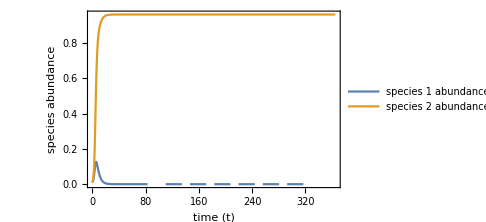
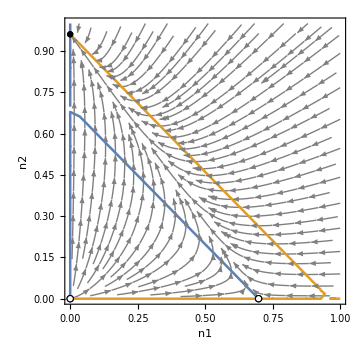

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

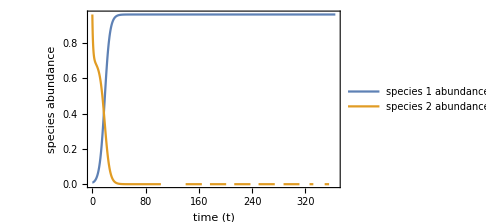
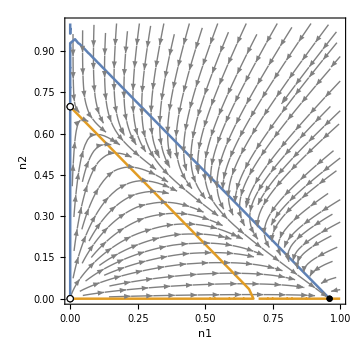

```mathematica
a12=1;
a21=1;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=1;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)

Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Tenv=10.5;
eq=SolveEcoEq[];
sol1=EcoSim[{n1->0.01,n2->0.01},365];
List[PlotDynamics[sol1,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"species 1 abundance","species 2 abundance"},ImageSize->Medium],
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Clear[Tenv];
Tenv=9.5;
eq=SolveEcoEq[];
sol2=EcoSim[{n1->0.01,n2->(n2/.FinalSlice[sol1])},365];
List[PlotDynamics[sol2,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"species 1 abundance","species 2 abundance"},ImageSize->Medium],
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
```

## coexistence

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

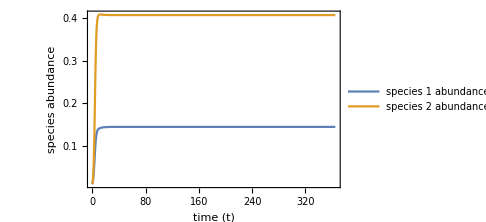
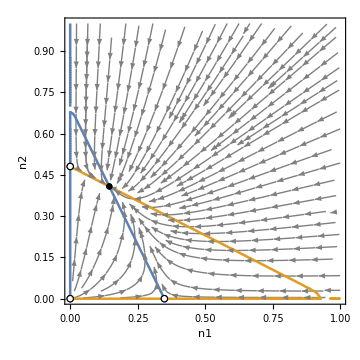

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

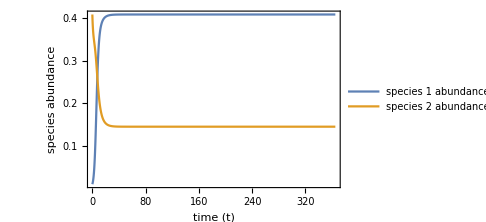
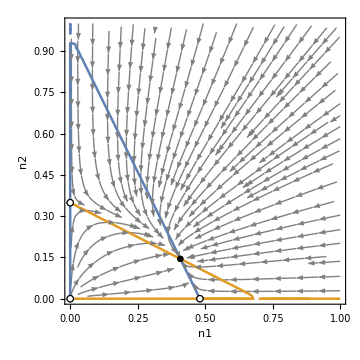

```mathematica
a12=1;
a21=1;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=2;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)

Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Tenv=10.5;
eq=SolveEcoEq[];
sol1=EcoSim[{n1->0.01,n2->0.01},365];
List[PlotDynamics[sol1,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"species 1 abundance","species 2 abundance"},ImageSize->Medium],
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Tenv=9.5;
eq=SolveEcoEq[];
sol2=EcoSim[{n1->0.01,n2->(n2/.FinalSlice[sol1])},365];
List[PlotDynamics[sol2,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"species 1 abundance","species 2 abundance"},ImageSize->Medium],
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
```

## founder control

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

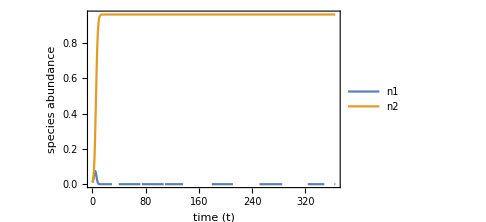

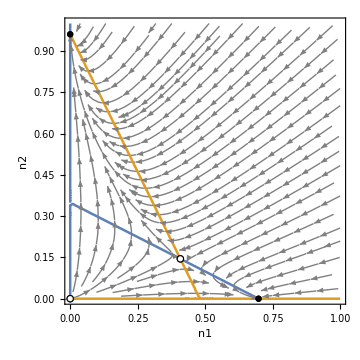

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

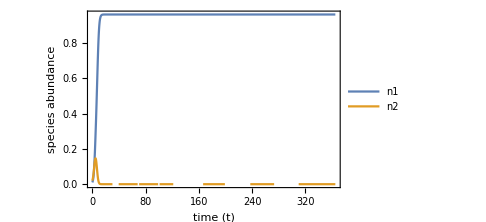

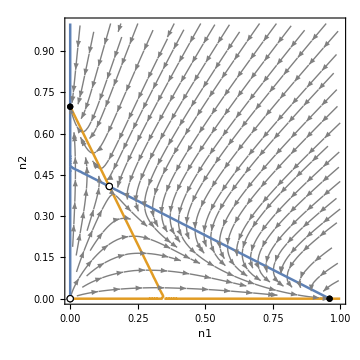

```mathematica
a12=2;
a21=2;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=1;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)

Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Tenv=10.5;
eq=SolveEcoEq[];
sol1=EcoSim[{n1->0.01,n2->0.01},365];
PlotDynamics[sol1,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"n1","n2"},ImageSize->Medium]
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
Topt1=9;(*temperature optimum of species n1*)
Topt2=11;(*temperature optimum of species n2*)
Tenv=9.5;
eq=SolveEcoEq[];
sol2=EcoSim[{n1->0.01,n2->0.02},365];
PlotDynamics[sol2,Frame->True,FrameLabel->{Style["time (t)",Bold,Black], Style["species abundance",Bold,Black]},PlotLegends->{"n1","n2"},ImageSize->Medium]
Show[
PlotEcoPhasePlane[{n1,0,r1},{n2,0,r2},ImageSize->Medium],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
```

# Timeseries and phase plane plots (variable temp.)

## Competition

$Aborted

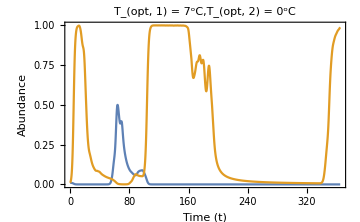

$Aborted

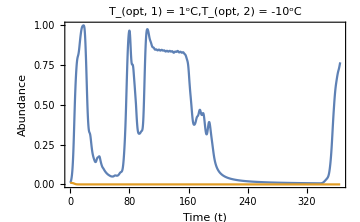

```mathematica
a12=1;
a21=1;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=1;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
Topt1=7;(*temperature optimum of species n1*)
Topt2=0;(*temperature optimum of species n2*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)
eq=SolveEcoEq[];
sol=EcoSim[{n1->0.01,n2->0.01},365];
PlotDynamics[sol,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = 7^oC,T_(opt, 2) = 0^oC",Black,FontSize->18]]

Topt1=1;(*temperature optimum of species n1*)
Topt2=-10;(*temperature optimum of species n2*)
eq=SolveEcoEq[];
sol=EcoSim[{n1->0.01,n2->0.01},365];
PlotDynamics[sol,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = 1^oC,T_(opt, 2) = -10^oC",Black,FontSize->18]]
```

## Coexistence

$Aborted

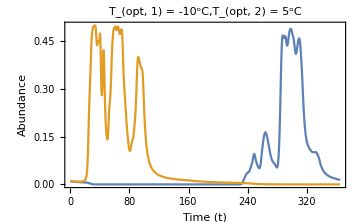

$Aborted

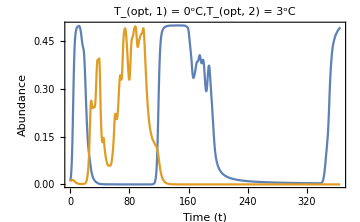

```mathematica
a12=1;
a21=1;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=2;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
Topt1=-10;(*temperature optimum of species n1*)
Topt2=5;(*temperature optimum of species n2*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)
eq=SolveEcoEq[];
sol=EcoSim[{n1->0.01,n2->0.01},365];
PlotDynamics[sol,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = -10^oC,T_(opt, 2) = 5^oC",Black,FontSize->18]]

Topt1=0;(*temperature optimum of species n1*)
Topt2=3;(*temperature optimum of species n2*)
eq=SolveEcoEq[];
sol=EcoSim[{n1->0.01,n2->0.01},365 ];
PlotDynamics[sol,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = 0^oC,T_(opt, 2) = 3^oC",Black,FontSize->18]]
```

## Founder control

$Aborted

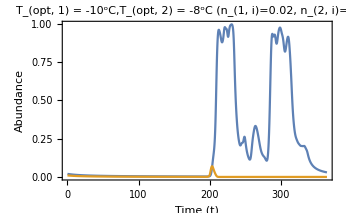

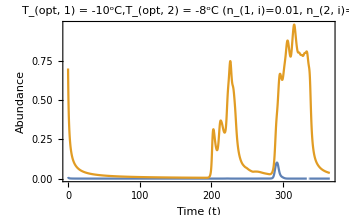

```mathematica
a12=a21=2;(*interspecific competition coefficients (competition between different speciess)*)
a11=a22=1;(*intraspecific competition coefficients (competition of one species with itself, leading to density dependence)*)
r1=1;(*growth rate of species n1*)
r2=1;(*growth rate of species n2*)
(*ambient temperature*)
Topt1=-10;(*temperature optimum of species n1*)
Topt2=-8;(*temperature optimum of species n2*)
σ1=2.5;(* width of temperature-response curve for n1 *)
σ2=2.5;(* width of temperature-response curve for n2 *)
eq=SolveEcoEq[];
sol1=EcoSim[{n1->.02,n2->0.01},365];
PlotDynamics[sol1,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = -10^oC,T_(opt, 2) = -8^oC (n_(1, i)=0.02, n_(2, i)=0.01)",Black,FontSize->18]]
sol2=EcoSim[{n1->0.01,n2->.7},365];
PlotDynamics[sol2,Frame->True,FrameLabel->{Style["Time (t)",Black,FontSize->18], Style["Abundance",Black,FontSize->18]},ImageSize->Medium,FrameTicksStyle->Directive[Black,12],PlotLabel->Style["T_(opt, 1) = -10^oC,T_(opt, 2) = -8^oC (n_(1, i)=0.01, n_(2, i)=0.7)",Black,FontSize->18]]
```

# RegionPlots

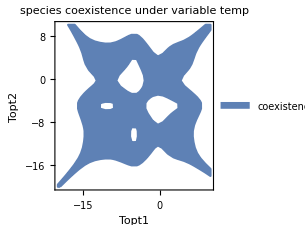
{1800.25,-Graphics-}

```mathematica
(*identifying region of coexistence*)
AbsoluteTiming[RegionPlot[{NIntegrate[(r2*a12/a22 E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]<NIntegrate[(r1 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]&&NIntegrate[(r1*a21/a11 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]<NIntegrate[(r2  E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]
},{Topt1,-20,10},{Topt2,-20,10},Frame->True,FrameLabel->{"Topt1","Topt2"},PlotLabel->"species coexistence under variable temp",PlotLegends->{"coexistence","species 1 wins","species 2 wins"},MaxRecursion->0,PlotStyle->ColorData[97,"ColorList"][[1]],BoundaryStyle->ColorData[97,"ColorList"][[1]],PlotPoints->30]]
```

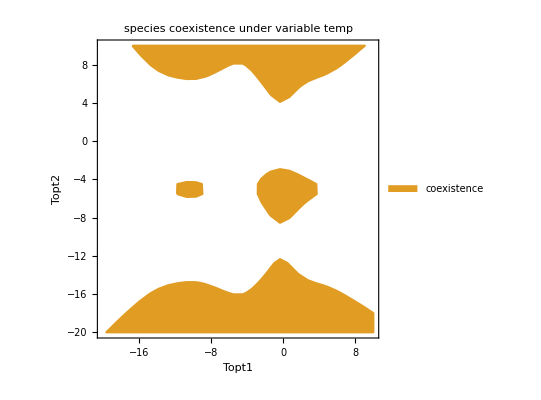
{929.521,-Graphics-}

```mathematica
(*Identifying the region of single-species dominance for species 1*)
AbsoluteTiming[RegionPlot[{NIntegrate[(r2*E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]<=NIntegrate[(r1 a21/a11 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]&&NIntegrate[(r1 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]>=NIntegrate[(r2 *a12/a22 E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]
},{Topt1,-20,10},{Topt2,-20,10},Frame->True,FrameLabel->{"Topt1","Topt2"},PlotLabel->"species coexistence under variable temp",PlotLegends->{"coexistence","species 1 wins","species 2 wins"},MaxRecursion->0,PlotStyle->ColorData[97,"ColorList"][[2]],BoundaryStyle->ColorData[97,"ColorList"][[2]],PlotPoints->30]]
```

```mathematica
(*Identifying the region of single-species dominance for species 2*)
```

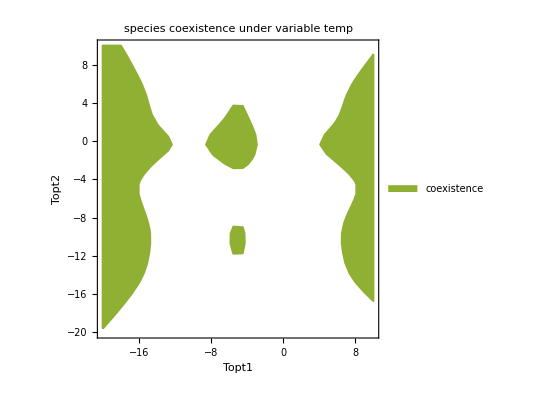
{1270.52,-Graphics-}

```mathematica
AbsoluteTiming[RegionPlot[{NIntegrate[(r2*E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]>=NIntegrate[(r1 a21/a11 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]&&NIntegrate[(r1 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]<=NIntegrate[(r2 *a12/a22 E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]
},{Topt1,-20,10},{Topt2,-20,10},Frame->True,FrameLabel->{"Topt1","Topt2"},PlotLabel->"species coexistence under variable temp",PlotLegends->{"coexistence","species 1 wins","species 2 wins"},MaxRecursion->0,PlotStyle->ColorData[97,"ColorList"][[3]],BoundaryStyle->ColorData[97,"ColorList"][[3]],PlotPoints->30]]
```

```mathematica
(*Identifying the region of founder control, which is equivalent to the region of coexistence with the parameters used for founder control*)
```

```mathematica
AbsoluteTiming[RegionPlot[{NIntegrate[(r2*a12/a22 E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]>NIntegrate[(r1 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]&&NIntegrate[(r1*a21/a11 E^(-(Topt1-(fourierfit[t]))^2/σ1^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]>NIntegrate[(r2  E^(-(Topt2-(fourierfit[t]))^2/σ2^2))/364,{t,0,364},Method->{Automatic,"SymbolicProcessing"->0}]
},{Topt1,-20,10},{Topt2,-20,10},Frame->True,FrameLabel->{"Topt1","Topt2"},PlotLabel->"species coexistence under variable temp",PlotLegends->{"coexistence","species 1 wins","species 2 wins"},MaxRecursion->0,PlotStyle->ColorData[97,"ColorList"][[1]],BoundaryStyle->ColorData[97,"ColorList"][[1]],PlotPoints->30]]
```

```mathematica
(*generating composite figure*)
```

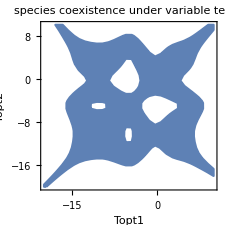
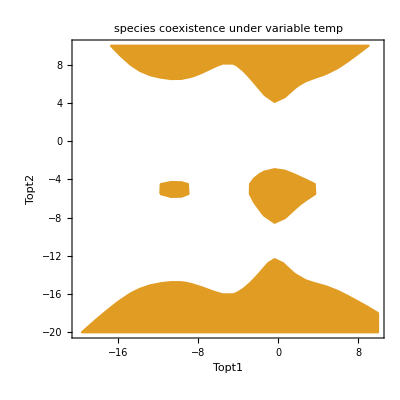
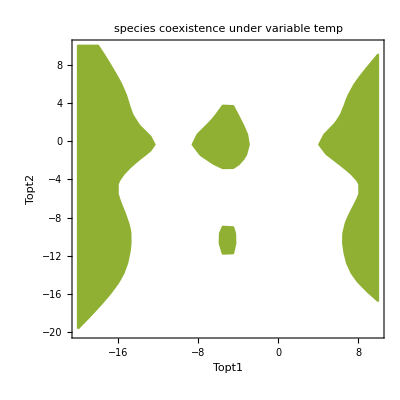
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```